```mathematica
ClearAll["Global`*"]; Remove["Global`*"];
```

```mathematica
r1=2; p1=Rationalize[0.4];
r2=3; p2=Rationalize[0.6];
```

```mathematica
pdfX1[x_] = Binomial[x-1,r1-1] p1^r1(1-p1)^(x-r1);
pdfX2[x_] = Binomial[x-1,r2-1] p2^r2(1-p2)^(x-r2);
```

```mathematica
pdfZ[z_] =∑_(x=r1)^(z-r2) pdfX1[x]pdfX2[z-x];
```

```mathematica
cdfZ[z_] =∑_(x=r1+r2)^z pdfZ[x];
```

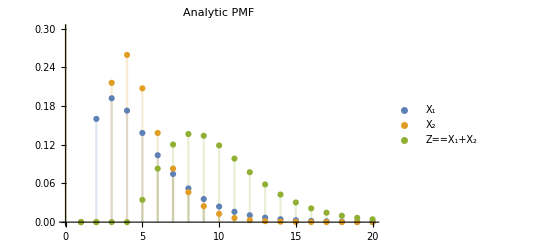

```mathematica
DiscretePlot[{pdfX1[x], pdfX2[x], pdfZ[x]}, {x, 0, 20},
PlotRange-> {0,0.3},
PlotLabel-> Style["Analytic PMF", FontWeight->Bold, FontColor-> Black],
PlotLegends-> {
ToExpression["X_1",TeXForm,HoldForm],
ToExpression["X_2",TeXForm,HoldForm],
ToExpression["Z=X_1+X_2",TeXForm,HoldForm]}]
```

```mathematica
(* Moment generating function *)
M[t_] =(p1 Exp[t])^r1/(1-(1-p1)Exp[t])^r1 (p2 Exp[t])^r2/(1-(1-p2)Exp[t])^r2 ;
```

```mathematica
(* Cumulant generating function *)
K[t_] = Log[M[t]];
K1[t_] =Simplify[D[K[t], t]];
K2[t_] = Simplify[D[K1[t], t]];
K3[t_] = Simplify[D[K2[t], t]];
K4[t_] = Simplify[D[K3[t], t]];
```

```mathematica
(* First order S.P.A. of PMF *)
pdfSPA1[x_]=Module[
{s=NSolve[{K1[z]==x},z, Reals][[1, 1, 2]]},
1/(√(2π K2[s]))Exp[K[s]-x s]];
```

```mathematica
re1=∑_(x=6)^500 pdfSPA1[x]
```

0.99276

```mathematica
(* Second order S.P.A. of PMF *)
pdfSPA2[x_]=Module[
{sHat=NSolve[{K1[z]==x},z, Reals][[1, 1, 2]]}, 
pdfSPA1[x](1+1/8 K4[sHat]/K2[sHat]^(4/2)-5/24(K3[sHat]/K2[sHat]^(3/2))^2)];
```

```mathematica
re2=∑_(x=6)^500 pdfSPA2[x]
```

0.964363

```mathematica
pdfSPA1re[x_] = pdfSPA1[x]/re1;
```

```mathematica
pdfSPA2re[x_] = pdfSPA2[x]/re2;
```

```mathematica
(* First order S.P.A. of CDF *)
cdfSPA[x_]=Module[{s,w,u,x=x+1}, (* increment x to account for strict inequality in SPA CDF (discrete) *)
s=NSolve[{K1[z]==x},z, Reals][[1, 1, 2]];
w=Sign[s]Sqrt[2s x-2K[s]];
u=(1-Exp[-s])Sqrt[K2[s]];
CDF[NormalDistribution[0,1], w] + PDF[NormalDistribution[0,1],  w](1/ w-1/u)
];
```

```mathematica
x = Range[6,30];
```

```mathematica
trueValues = N[Map[pdfZ, x]];
```

```mathematica
spa1Values = Map[pdfSPA1, x];
```

```mathematica
spa2Values = Map[pdfSPA2, x];
```

```mathematica
Grid[Transpose[{Flatten[{"True", trueValues}],Flatten[{"SPA 1st",spa1Values}],Flatten[{"SPA 2nd",spa2Values}]}], Frame-> All]
```

True | SPA 1st | SPA 2nd
0.082944 | 0.0901188 | 0.0824519
0.120269 | 0.125693 | 0.120148
0.136581 | 0.140835 | 0.136561
0.133872 | 0.137072 | 0.133884
0.118909 | 0.121207 | 0.118915
0.0984601 | 0.100052 | 0.0984418
0.0773834 | 0.0784604 | 0.0773392
0.0584337 | 0.0591555 | 0.0583721
0.0427607 | 0.0432457 | 0.0426931
0.0305159 | 0.0308454 | 0.0304516
0.0213383 | 0.0215655 | 0.0212829
0.014673 | 0.0148319 | 0.0146286
0.00995014 | 0.0100623 | 0.00991658
0.00666903 | 0.00674861 | 0.00664472
0.00442583 | 0.00448228 | 0.00440883
0.00291242 | 0.0029523 | 0.00290087
0.00190262 | 0.00193062 | 0.00189495
0.00123512 | 0.00125462 | 0.00123013
0.000797405 | 0.00081087 | 0.000794209
0.000512329 | 0.000521545 | 0.000510309
0.000327767 | 0.000334022 | 0.000326504
0.000208899 | 0.000213109 | 0.000208117
0.00013269 | 0.000135502 | 0.000132209
0.0000840276 | 0.0000858925 | 0.0000837333
0.0000530661 | 0.0000542947 | 0.000052887

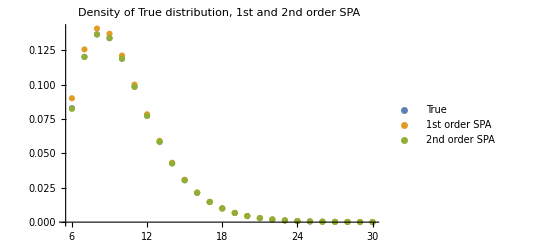

```mathematica
ListPlot[{Thread[{x, trueValues}],Thread[{x, spa1Values}],Thread[{x,spa2Values}]}, PlotLegends ->{"True", "1st order SPA", "2nd order SPA"}, PlotLabel-> Style["Density of True distribution, 1st and 2nd order SPA", FontWeight->Bold, FontColor-> Black]]
```

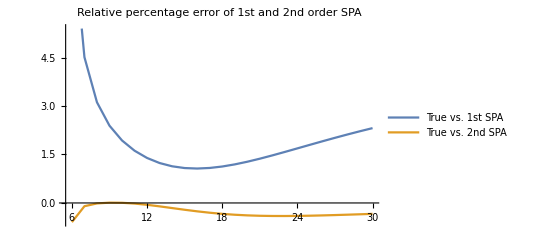

```mathematica
ListLinePlot[{
Thread[{x, 100(spa1Values - trueValues)/trueValues}],
Thread[{x, 100(spa2Values - trueValues)/trueValues}]
},
PlotLegends-> {"True vs. 1st SPA", "True vs. 2nd SPA"},
PlotLabel-> Style["Relative percentage error of 1st and 2nd order SPA", FontWeight-> Bold, FontColor -> Black]]
```

```mathematica
Print["True: Probability of having more than 8 kids: ", N[1-cdfZ[8]]]
Print["True: Probability of having more than 12 kids: ", N[1-cdfZ[12]]]
```

True: Probability of having more than 8 kids: 0.625646

True: Probability of having more than 12 kids: 0.197022

```mathematica
Print["1st order SPA: Probability of having more than 8 kids: ", 1-cdfSPA[8]]
Print["1st order SPA: Probability of having more than 12 kids: ", 1-cdfSPA[12]]
```

1st order SPA: Probability of having more than 8 kids: 0.624017

1st order SPA: Probability of having more than 12 kids: 0.196042